```mathematica
Table[Sin[Pi/x], {x, 1, 52}]
```

{0,1,(√3)/2,1/(√2),√(5/8-(√5)/8),1/2,Sin[π/7],Sin[π/8],Sin[π/9],1/4 (-1+√5),Sin[π/11],(-1+√3)/(2 √2),Sin[π/13],Sin[π/14],Sin[π/15],Sin[π/16],Sin[π/17],Sin[π/18],Sin[π/19],Sin[π/20],Sin[π/21],Sin[π/22],Sin[π/23],Sin[π/24],Sin[π/25],Sin[π/26],Sin[π/27],Sin[π/28],Sin[π/29],Sin[π/30],Sin[π/31],Sin[π/32],Sin[π/33],Sin[π/34],Sin[π/35],Sin[π/36],Sin[π/37],Sin[π/38],Sin[π/39],Sin[π/40],Sin[π/41],Sin[π/42],Sin[π/43],Sin[π/44],Sin[π/45],Sin[π/46],Sin[π/47],Sin[π/48],Sin[π/49],Sin[π/50],Sin[π/51],Sin[π/52]}

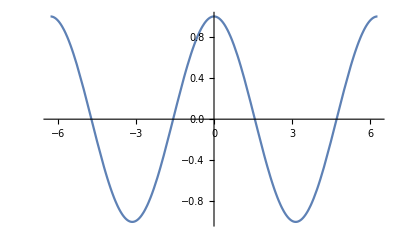

```mathematica
Plot[Cos[x], {x, -2*Pi, 2*Pi}]
```

```mathematica
cos[0]=1;
cos[Pi]=-1;
cos[Pi*n_Integer]=(-1)^n;
cos[Pi*r_Rational]=
Which[
r<0, cos[-r*Pi],
r>2, cos[Mod[r, 2]*Pi],
r>1, cos[(2-r)*Pi],
r > 1/2, -cos[(1-r)*Pi],
EvenQ[Denominator[r]], Sqrt[(1+cos[2*r*Pi])/2],
True, Cos[r*Pi]
];
```

```mathematica
y=3*Pi/8;
{Cos[y], cos[y]}
```

{Sin[π/8],√(1/2 (1-1/(√2)))}

```mathematica
Max[Table[Table[N[Abs[Cos[m*Pi/n]-cos[m*Pi/n]]],{m,-128,128}],{n,1,128}]]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4 (1-√5)+1/4 (-1+√5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/4 (-1-√5)+1/4 (1+√5).

General::stop: Further output of N::meprec will be suppressed during this calculation.

7.84095×10^-16

```mathematica
sin[x_]=cos[x-Pi/2];
```

```mathematica
y=3*Pi/8;
{Sin[y], sin[y]}
```

{Cos[π/8],√(1/2 (1+1/(√2)))}

```mathematica
Max[Table[Table[N[Abs[Sin[m*Pi/n]-sin[m*Pi/n]]],{m,-128,128}],{n,1,128}]]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(5/8+(√5)/8)-√(1/2 (1+1/4 (1+Power[«2»]))).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(5/8-(√5)/8)-√(1/2 (1+1/4 (1+Times[«2»]))).

General::stop: Further output of N::meprec will be suppressed during this calculation.

7.84095×10^-16

```mathematica
Table[sin[Pi/x], {x, 1, 52}]
```

{0,1,(√3)/2,1/(√2),√(1/2 (1+1/4 (1-√5))),1/2,√(1/2 (1-Sin[(3 π)/14])),√(1/2 (1-1/(√2))),√(1/2 (1-Cos[(2 π)/9])),1/4 (-1+√5),√(1/2 (1-Cos[(2 π)/11])),√(1/2 (1-(√3)/2)),√(1/2 (1-Cos[(2 π)/13])),Sin[π/14],√(1/2 (1-Cos[(2 π)/15])),√(1/2 (1-√(1/2 (1+1/(√2))))),√(1/2 (1-Cos[(2 π)/17])),Sin[π/18],√(1/2 (1-Cos[(2 π)/19])),√(1/2 (1-√(1/2 (1+1/4 (1+√5))))),√(1/2 (1-Cos[(2 π)/21])),Sin[π/22],√(1/2 (1-Cos[(2 π)/23])),√(1/2 (1-√(1/2 (1+(√3)/2)))),√(1/2 (1-Cos[(2 π)/25])),Sin[π/26],√(1/2 (1-Cos[(2 π)/27])),√(1/2 (1-√(1/2 (1+Cos[π/7])))),√(1/2 (1-Cos[(2 π)/29])),Sin[π/30],√(1/2 (1-Cos[(2 π)/31])),1/(√(2/(1-√(1/2 (1+√(1/2 (1+1/(√2)))))))),√(1/2 (1-Cos[(2 π)/33])),Sin[π/34],√(1/2 (1-Cos[(2 π)/35])),√(1/2 (1-√(1/2 (1+Cos[π/9])))),√(1/2 (1-Cos[(2 π)/37])),Sin[π/38],√(1/2 (1-Cos[(2 π)/39])),1/(√(2/(1-√(1/2 (1+√(1/2 (1+1/4 (1+√5)))))))),√(1/2 (1-Cos[(2 π)/41])),Sin[π/42],√(1/2 (1-Cos[(2 π)/43])),√(1/2 (1-√(1/2 (1+Cos[π/11])))),√(1/2 (1-Cos[(2 π)/45])),Sin[π/46],√(1/2 (1-Cos[(2 π)/47])),1/(√(2/(1-√(1/2 (1+√(1/2 (1+(√3)/2))))))),√(1/2 (1-Cos[(2 π)/49])),Sin[π/50],√(1/2 (1-Cos[(2 π)/51])),√(1/2 (1-√(1/2 (1+Cos[π/13]))))}